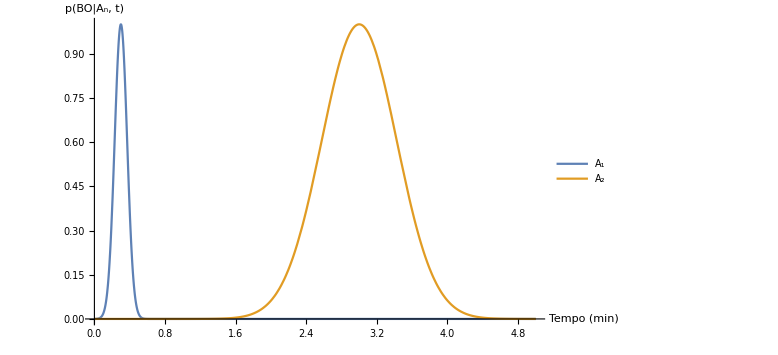

```mathematica
prob1=Plot[{
Exp[-(t-0.3)^2/Power[0.1, 2]],
Exp[-(t-3)^2/Power[0.6, 2]]
}, {t, 0, 5},
PlotRange->Full,
AxesLabel->{"Tempo (min)","p(BO|A_n, t)"},
PlotLegends->{"A_1", "A_2"},
ImageSize->Large
]
Export[NotebookDirectory[]<>"Distribuicao1.pdf", prob1];
```